## Quartic Integral (1.3.11)

```mathematica
(1/Sqrt[2π]) Integrate[Exp[-z^2/2 - g z^4/4], {z,-∞,∞}]
```

ConditionalExpression[(ⅇ^(1/8/g) BesselK[1/4,1/(8 g)])/(2 √g √π), Re[g]>0]

## Definitions

```mathematica
quarticI[g_]:=(ⅇ^(1/8/g) BesselK[1/4,1/(8 g)])/(2 √g √π)
(*quarticIseries[g_, nmax_]:= Expand[(1/Sqrt[2π]) Distribute[Integrate[Normal[Series[Exp[-z^2/2 - g z^4/4], {g,0,nmax}]], {z,-∞,∞}]]]*)
quarticIseries[g_,nmax_]:=Sum[((-1)^n Gamma[1/2+2 n])/(√π n!) g^n, {n,0,nmax}]
```

```mathematica
boreltransf[series_,u_,nmax_]:=Module[{coefs,g}, coefs=CoefficientList[series[g,nmax], g];Sum[coefs[[n]] u^(n-1) / Factorial[n-1], {n,Length[coefs]}]]
borelpade[series_,u_,nmax_]:=PadeApproximant[boreltransf[series,u,nmax], {u,0,{Floor[nmax/2],Floor[(nmax+1)/2]}}]
```

```mathematica
(* For Borel transform B[u] as a function of u only *)
zerosplot[borel_,color_:Blue]:=Module[{zeros}, zeros=u/.NSolve[borel==0,u];Print[zeros];ComplexListPlot[zeros,PlotStyle->Directive[color,PointSize[0.02]]]]
polesplot[borel_]:=zerosplot[1/borel, Red]
borelresum[borel_,g_?NumericQ]:=(1/g)NIntegrate[Exp[-u/g] borel, {u,0,∞}]
```

## Figure 3.1

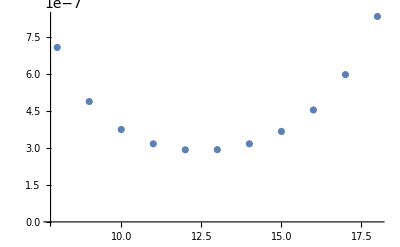

```mathematica
Table[{n, quarticI[g] - quarticIseries[g,n]}, {n,8,18}];
ListPlot[Abs[% /. g->0.02]]
```

## Example 3.4

```mathematica
(1/Sqrt[2π]) Integrate[Limit[D[Exp[-z^2/2 - g z^4/4], {g,n}] / Factorial[n], g->0], {z,-∞,∞}]
Sum[% u^n / Factorial[n], {n,0,∞}]
quarticI[0.2]
borelresum[%%, 0.2]
quarticIseries[g,1] /. g->0.2
```

ConditionalExpression[((-1)^n Gamma[1/2+2 n])/(√π n!), Re[n]>-1/4]

(2 EllipticK[(-1+√(1+4 u))/(2 √(1+4 u))])/(π (1+4 u)^(1/4))

0.907985

0.907985

0.85

## Table 3.1

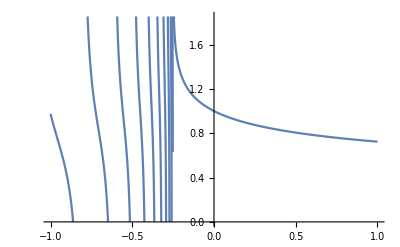

{-60.7103,-9.33987,-3.63888,-1.94901,-1.23113,-0.861916,-0.648204,-0.514354,-0.425866,-0.365221,-0.322799,-0.293014,-0.272497,-0.259203,-0.251929}

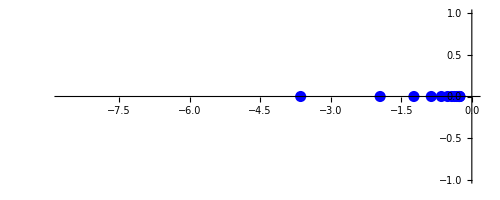

{-32.0488,-7.1462,-3.09185,-1.74073,-1.13247,-0.808605,-0.616808,-0.494764,-0.413172,-0.356821,-0.31722,-0.289375,-0.270249,-0.257987,-0.25149}

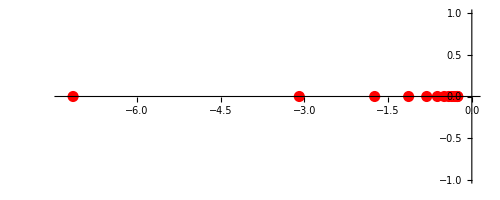

```mathematica
pade=borelpade[quarticIseries, u, 30];
Plot[pade, {u,-1,1}]
 (*zeros*)
zerosplot[pade]
(*poles*)
polesplot[pade]
```

Branch point at u = -1/4

```mathematica
borelresum[pade,0.2]
borelresum[pade,0.4]
```

0.907985

0.857609

```mathematica
nmax = 10
0.9079854376030722
0.8576207822712806
```

```mathematica
nmax = 20
0.9079847775740948
0.8576086008255066
```

```mathematica
nmax = 30
0.9079847774309506
0.8576085853876735
```

## Accuracy

### quartic integral and approximations

For the quartic integral I(g), Eq. (1.3.11), we define a truncated series

ϕ_n(g) = ∑_(k=0)^n a_k g^k.

Then, we can use the Borel-Pade resummation

(s(ϕ))_n(g) = g^-1 ∫ⅇ^(-u/g)(P^ϕ)_n(u) ⅆu,
(P^ϕ)_n(u) = [[n/2]/[(n+1)/2]]_(ϕ̂)(u),

and the Pade approximant for ϕ_n

(R^ϕ)_n(g) = [[n/2]/[(n+1)/2]]_ϕ(g).

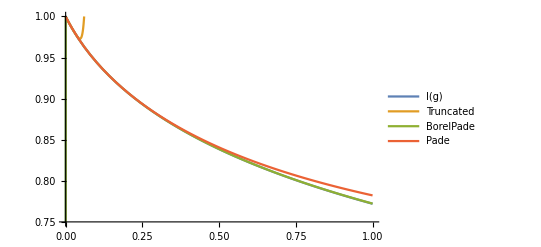

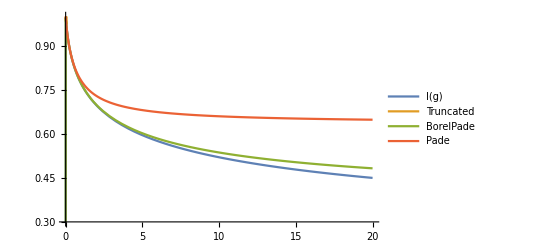

```mathematica
nmax=10;
pade1=borelpade[quarticIseries,u,nmax];
pade2=PadeApproximant[quarticIseries[g,nmax], {g,0,{Floor[nmax/2],Floor[(nmax+1)/2]}}];
Plot[{quarticI[g], Evaluate[quarticIseries[g,nmax]],borelresum[pade1,g],pade2}, {g,0,1}, PlotRange->{Automatic,{0.75,1}}, PlotLegends->{"I(g)", "Truncated", "BorelPade", "Pade"}]
Plot[{quarticI[g], Evaluate[quarticIseries[g,nmax]],borelresum[pade1,g],pade2}, {g,0,20}, PlotRange->{Automatic,{0.3,1}}, PlotLegends->{"I(g)", "Truncated", "BorelPade", "Pade"}]
```

```mathematica
(1/Sqrt[2π]) Integrate[Exp[- g z^4/4], {z,-∞,∞}]
Series[quarticI[g], {g,∞,1}]
N[Series[pade2, {g,∞,1}]]
```

ConditionalExpression[Gamma[1/4]/(2 g^(1/4) √π), Re[g]>0]

(Gamma[1/4] (1/g)^(1/4))/(2 √π)+(Gamma[-1/4] (1/g)^(3/4))/(8 √π)+O[1/g]^(5/4)

0.451709+1.23804/g+O[1/g]^2

### (R^ϕ)_n and ϕ_n

```mathematica
nmax=40;
gval=0.2;
PadeApproximant[quarticIseries[g,nmax], {g,0,{Floor[nmax/2],Floor[(nmax+1)/2]}}];
ListPlot[Table[{n, Abs[quarticIseries[gval,nmax]] - Abs[Normal[Series[%, {g,0,n}]]/.g->gval]}, {n,nmax,Sqrt[2]nmax}]]
```

-Graphics-

{-1.54066,-0.325884,-0.134987,-0.0725012,-0.0446346,-0.0298337,-0.0210188,-0.0153092,-0.011339}

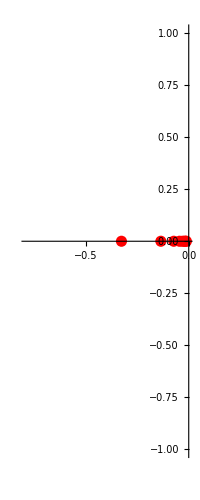

```mathematica
nmax=20;
PadeApproximant[quarticIseries[g,nmax], {g,0,{Floor[nmax/2],Floor[(nmax+1)/2]}}];
polesplot[%/.g->u]
```

### (P^ϕ)_n and ϕ̂

```mathematica
quarticIborel[u_]:=(2 EllipticK[(-1+√(1+4 u))/(2 √(1+4 u))])/(π (1+4 u)^(1/4))
```

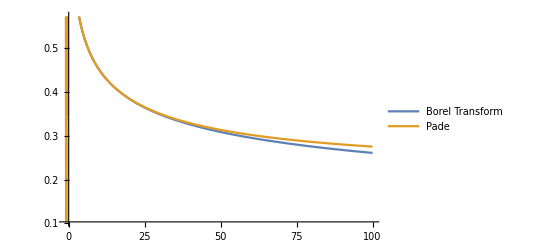

```mathematica
pade3=borelpade[quarticIseries, u, 30];
Plot[{quarticIborel[u],pade3}, {u,-1,100},PlotLegends->{"Borel Transform", "Pade"}]
```

```mathematica
Series[quarticIborel[u], {u,∞,1}]
N[Series[pade3, {u,∞,1}]]
```

(Gamma[1/4] (1/u)^(1/4))/(2 √π Gamma[3/4])+(Gamma[-1/4] (1/u)^(3/4))/(32 √π Gamma[5/4])+O[1/u]^(5/4)

0.219471+6.98965/u+O[1/u]^2

## Optimized perturbation theory

We consider the delta expansion (or optimized perturbation theory).

```mathematica
(1/Sqrt[2π]) Integrate[Exp[-α z^2/2 + δ((α-1) z^2/2 - g z^4/4)], {z,-∞,∞}]
```

ConditionalExpression[(ⅇ^((α+δ-α δ)^2/(8 g δ)) √(α+δ-α δ) BesselK[1/4,(α+δ-α δ)^2/(8 g δ)])/(2 √π √(g δ)), Re[g δ]>0&&Re[α+δ-α δ]>0]

The expansion is done with respect to δ and we will set δ=1 finally, as

∑_(k=0)^n a_k(α,g)δ^k|_(δ→1).

We use the condition to fix the adjustable parameter α,

a_n(α,g)=0.

(fastest apparent convergence condition)

### Numerical

{ConditionalExpression[1/(√α), Re[α]>0],ConditionalExpression[(-0.0375994-1.25331 α+1.25331 α^2)/(√(2 π) α^(5/2)), Re[α]>0]}

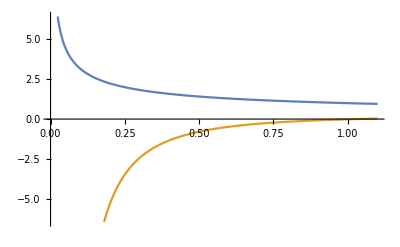

{α→1.02915}

{0.985736,-3.04504×10^-17}

{0.985736,0.000922645}

0.986136

```mathematica
nmax=1;
gval=0.02;
Table[(1/Sqrt[2π]) Integrate[Limit[D[Exp[-α z^2/2 + δ((α-1) z^2/2 - gval z^4/4)], {δ,n}] / Factorial[n], δ->0], {z,-∞,∞}], {n, 0, nmax}]
Plot[%, {α,0,1.1}]
Flatten[NSolve[%%[[-1]]==0,α, Reals]]
αval = α/.%;
Table[(1/Sqrt[2π]) Integrate[Limit[D[Exp[-αval z^2/2 + δ((αval-1) z^2/2 - gval z^4/4)], {δ,n}] / Factorial[n], δ->0], {z,-∞,∞}], {n, 0, nmax}]
(* ∑_(k=0)^n Subscript[a, k] δ^k with δ->1 and the magnitude of error Subscript[a, n+1]*)
{Total[%], (1/Sqrt[2π]) Integrate[Limit[D[Exp[-αval z^2/2 + δ((αval-1) z^2/2 - gval z^4/4)], {δ,nmax+1}] / Factorial[nmax], δ->0], {z,-∞,∞}]}
quarticI[gval]
```

```mathematica
opt[g_,nmax_,printfac_:0]:=Module[{α,αval,δ,lastcoef, fac},lastcoef=Integrate[Exp[-α z^2/2]((α-1) z^2/2 - g z^4/4)^nmax / Factorial[nmax], {z,-∞,∞}];
fac=Flatten[NSolve[lastcoef==0,α, Reals]];
If[printfac≠0,Print[{g,nmax,fac}]];
αval = α/.fac;
Sum[(1/Sqrt[2π]) Integrate[Limit[D[Exp[-αval z^2/2 + δ((αval-1) z^2/2 - g z^4/4)], {δ,n}] / Factorial[n], δ->0], {z,-∞,∞}], {n, 0, nmax}]]
```

```mathematica
opt[0.02,3,1]
```

{0.02,3,{α$1747483→1.07691}}

0.986134

{{0.02,0.985736},{0.12,0.930185},{0.22,0.890314},{0.32,0.859264},{0.42,0.833889},{0.52,0.812474},{0.62,0.793981},{0.72,0.777732},{0.82,0.763258},{0.92,0.750224}}

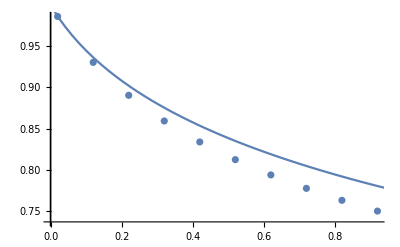

```mathematica
ParallelTable[{gval,opt[gval,1]}, {gval, 0.02, 1, 0.1}]
Show[ListPlot[%], Plot[quarticI[g], {g,0,1}]]
```

```mathematica
ParallelTable[{gval,opt[gval,3]}, {gval, 1, 20}]
Show[ListPlot[%], Plot[quarticI[g], {g,0,20}]]
```

```mathematica
(* nmax = 3 *)
optlist1={{0.02,0.9861344683039575},{0.04,0.9740327626833248},{0.06,0.9632110717222165},{0.08,0.9533803627561077},{0.1,0.9443491363705213},{0.12000000000000001,0.935981625744258},{0.14,0.928176889885563},{0.16,0.9208571929232434},{0.18,0.9139610243976898},{0.2,0.9074386517161251},{0.22,0.9012491512877909},{0.24,0.895358351099655},{0.26,0.8897373603357869},{0.28,0.8843614911191879},{0.30000000000000004,0.8792094503209528},{0.32000000000000006,0.8742627222936661},{0.34,0.8695050896530963},{0.36000000000000004,0.8649222558546282},{0.38,0.8605015441385613},{0.4,0.8562316546526988},{0.42,0.8521024665037745},{0.44,0.8481048749349899},{0.46,0.8442306562722449},{0.48000000000000004,0.8404723550452172},{0.5,0.8368231889800783},{0.52,0.833276968517791},{0.54,0.8298280282304905},{0.56,0.8264711680539159},{0.5800000000000001,0.8232016026722351},{0.6000000000000001,0.8200149177155558},{0.62,0.8169070316834769},{0.64,0.8138741627073507},{0.66,0.8109127994221162},{0.6799999999999999,0.8080196753450115},{0.7000000000000001,0.8051917462602327},{0.7200000000000001,0.8024261701910174},{0.7400000000000001,0.7997202896077519},{0.76,0.7970716155757074},{0.78,0.7944778135912884},{0.8,0.7919366908931653},{0.8200000000000001,0.7894461850658362},{0.8400000000000001,0.7870043537791933},{0.86,0.7846093655295189},{0.88,0.7822594912657338},{0.9,0.779953096800274},{0.9199999999999999,0.7776886359171816},{0.9400000000000001,0.77546464410124},{0.9600000000000001,0.7732797328215897},{0.9800000000000001,0.7711325843115113},{1.,0.7690219467931384}};
```

```mathematica
(* nmax = 3 *)
optlist2={{1,0.7690219467931383},{2,0.6934194564149146},{3,0.6475885614156349},{4,0.6150099251296464},{5,0.589922130723625},{6,0.5696351699353551},{7,0.5526775759370567},{8,0.5381583006917874},{9,0.5254978214385961},{10,0.5142986475769007},{11,0.5042766729619094},{12,0.4952220338003639},{13,0.48697547278902853},{14,0.47941338833949376},{15,0.4724380071679842},{16,0.4659707122295267},{17,0.4599473860133505},{18,0.4543150818862879},{19,0.4490295945800399},{20,0.44405365404042985}};
```

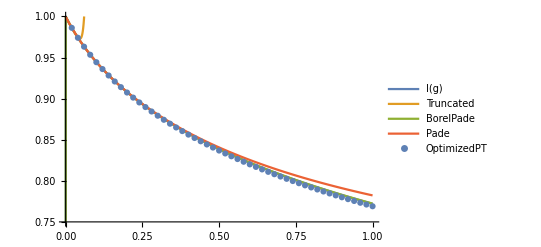

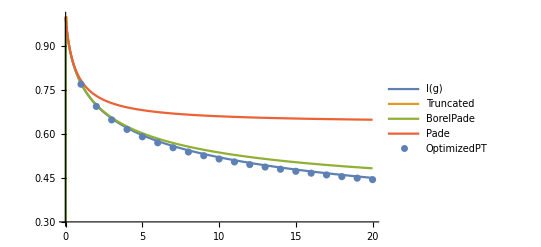

```mathematica
Show[-Graphics-,
ListPlot[optlist1, PlotLegends->{"OptimizedPT"}]]
Show[-Graphics-,
ListPlot[optlist2, PlotLegends->{"OptimizedPT"}]]
```

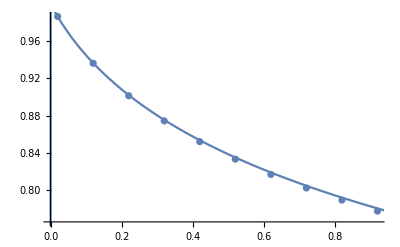
{-Graphics-,-Graphics-}

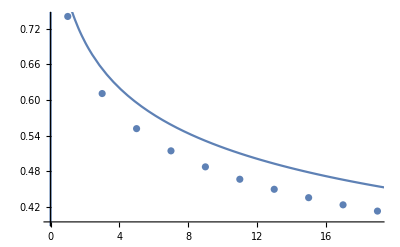
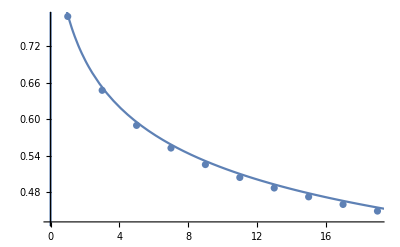
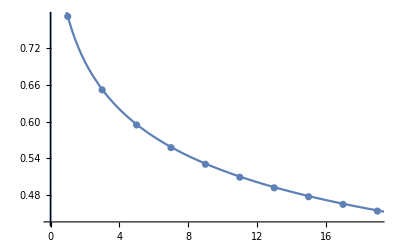

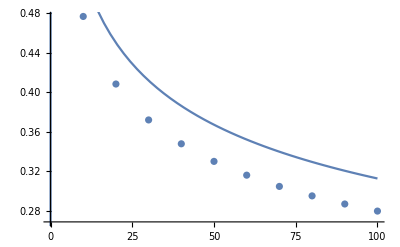
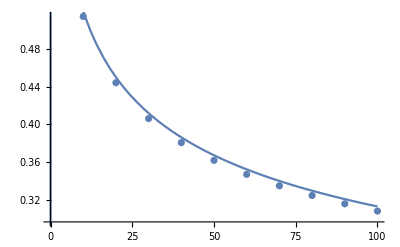
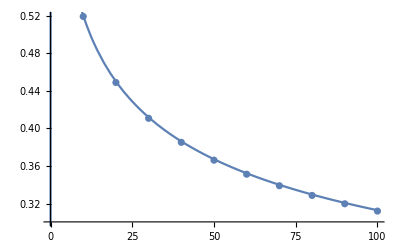
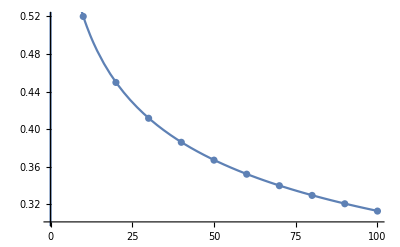

```mathematica
Table[tab=ParallelTable[{gval,opt[gval,nmax]}, {gval, 0.02, 1, 0.1}];
Show[ListPlot[tab], Plot[quarticI[g], {g,0,1}]], {nmax,1,3,2}]

Table[tab=ParallelTable[{gval,opt[gval,nmax]}, {gval, 1, 20, 2}];
Show[ListPlot[tab], Plot[quarticI[g], {g,0,20}]], {nmax,1,5,2}]

Table[tab=ParallelTable[{gval,opt[gval,nmax]}, {gval, 10, 100, 10}];
Show[ListPlot[tab], Plot[quarticI[g], {g,0,100}]], {nmax,1,7,2}]
```

### Symbolic

```mathematica
N[Limit[g^(1/4)quarticI[g], g->∞]]
```

1.02277

```mathematica
optcoef[n_,α_,g_]:=(1/Sqrt[2π]) Integrate[Exp[-α z^2/2]((α-1) z^2/2 - g z^4/4)^n, {z,-∞,∞}, Assumptions->g>0] / Factorial[n]
```

ConditionalExpression[-(5 (693 g^3-378 g^2 (-1+α) α+84 g (-1+α)^2 α^2-8 (-1+α)^3 α^3))/(128 α^(13/2)), Re[α]>0]

{α→ConditionalExpression[1/2 (1+√(1+g Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101)), g>0]}

ConditionalExpression[(11.3137+11.3137 √(1.+16.5661 g)+g (202.367+555.959 g+108.655 √(1.+16.5661 g)))/(1.+√(1.+16.5661 g))^(9/2), g>0]

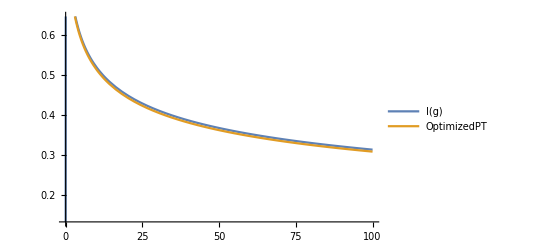

0.0186178

ConditionalExpression[(1575 g^4 Root74.1Root[-1824768+13824 #1+72 #1^2+#1^3&,1]74.05610331559343)/(8 √2 (1+√(1+g Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^(17/2)), g>0]

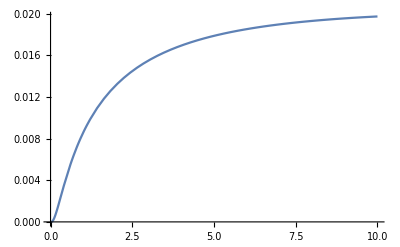

0.0678503

```mathematica
nmax=3;
optcoef[nmax, α, g]
FullSimplify[Flatten[Solve[%==0&&g>0&&α>0,α]]]
αsol = α/.%;
optg = FullSimplify[Sum[N[optcoef[n,αsol,g]], {n,0,nmax-1}]]

Plot[{quarticI[g], optg}, {g,0,100}, PlotLegends->{"I(g)", "OptimizedPT"}]
(* g->∞ *)
1.0227656721131686 - N[Limit[g^(1/4)optg, g->∞]]

(* error *)
FullSimplify[optcoef[nmax+1,αsol,g]]
Plot[%, {g,0,10}]
N[Limit[g^(1/4)%%,g-> ∞]]
```

#### Delta expansion as a special case of ODM

```mathematica
(*γ=gp/g*)
Solve[1 == γ δ / (α-δ(α-1))^2 && γ>0&&α>0&&δ>0, δ]
```

{{δ→ConditionalExpression[(-2 α+2 α^2+γ)/(2 (-1+α)^2)-1/2 √((-4 α γ+4 α^2 γ+γ^2)/(-1+α)^4), (α>1&&γ>0)||(0<α<1&&γ>4 α-4 α^2)]},{δ→ConditionalExpression[(-2 α+2 α^2+γ)/(2 (-1+α)^2)+1/2 √((-4 α γ+4 α^2 γ+γ^2)/(-1+α)^4), (α>1&&γ>0)||(0<α<1&&γ>4 α-4 α^2)]}}

```mathematica
δsol[α_,γ_] := (-2 α+2 α^2+γ)/(2 (-1+α)^2)-1/2 √((-4 α γ+4 α^2 γ+γ^2)/(-1+α)^4)
```

```mathematica
FullSimplify[δsol[α,0], Assumptions->α>1]
FullSimplify[δsol[α,1], Assumptions->α>1]
Limit[δsol[α,γ], γ->∞,Assumptions->α>1]
```

α/(-1+α)

1

0

ConditionalExpression[-(5 (693 gp^3-378 gp^2 (-1+α) α+84 gp (-1+α)^2 α^2-8 (-1+α)^3 α^3))/(128 α^(13/2)), Re[α]>0]

{α→ConditionalExpression[1/2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101)), gp>0]}

ConditionalExpression[(4 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^4+2 gp δ (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^2 Root10.6Root[-2304+360 #1-24 #1^2+#1^3&,1]10.566088107451007+gp^2 δ^2 Root125.Root[-5854464+252 #1^2+#1^3&,1]124.67026955221434)/(2 √2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^(9/2)), gp>0]

ConditionalExpression[(0.353553 √(0.5 (1.+√(1.+16.5661 g γ))-1. (-1.+0.5 (1.+√(1.+16.5661 g γ))) ((0.5 (-1.+γ-1. √(1.+16.5661 g γ)+0.5 (1.+√(1.+16.5661 g γ))^2))/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^2-0.5 √((γ^2-2. γ (1.+√(1.+16.5661 g γ))+γ (1.+√(1.+16.5661 g γ))^2)/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^4))) (4. (1.+√(1.+16.5661 g γ))^4+21.1322 g γ (1.+√(1.+16.5661 g γ))^2 ((0.5 (-1.+γ-1. √(1.+16.5661 g γ)+0.5 (1.+√(1.+16.5661 g γ))^2))/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^2-0.5 √((γ^2-2. γ (1.+√(1.+16.5661 g γ))+γ (1.+√(1.+16.5661 g γ))^2)/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^4))+124.67 g^2 γ^2 ((0.5 (-1.+γ-1. √(1.+16.5661 g γ)+0.5 (1.+√(1.+16.5661 g γ))^2))/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^2-0.5 √((γ^2-2. γ (1.+√(1.+16.5661 g γ))+γ (1.+√(1.+16.5661 g γ))^2)/(-1.+0.5 (1.+√(1.+16.5661 g γ)))^4))^2))/(1.+√(1.+16.5661 g γ))^(9/2), g γ>0.]

-Graphics-

ConditionalExpression[1.02277, !(γ≤0.&&γ≤0.)]

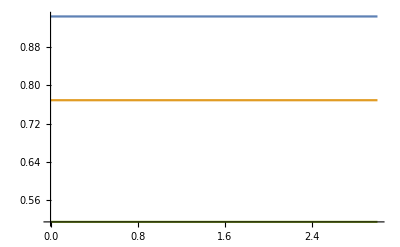

ConditionalExpression[(1575 gp^4 Root74.1Root[-1824768+13824 #1+72 #1^2+#1^3&,1]74.05610331559343)/(8 √2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^(17/2)), gp>0]

-Graphics-

0.0678503

```mathematica
nmax=3;
optcoef[nmax, α, gp]
FullSimplify[Flatten[Solve[%==0&&gp>0&&α>0,α]]]
αsol = α/.%;
FullSimplify[Sum[optcoef[n,αsol,gp]δ^n, {n,0,nmax-1}]]
optg=N[(((αsol-δ(αsol-1))^(1/2)%)/.δ->δsol[αsol,γ]) /. gp->γ g]

Plot[{quarticI[g], optg/.γ->1}, {g,0,100}, PlotLegends->{"I(g)", "OptimizedPT"}]
(* g->∞ *)
1.0227656721131686 - N[Limit[g^(1/4)optg, g->∞]]

(* γ-independence *)
Plot[{optg/.g->0.1, optg/.g->1,optg/.g->10}, {γ,0,3}]

(* error *)
FullSimplify[optcoef[nmax+1,αsol,gp]]
Plot[%, {gp,0,10}]
N[Limit[gp^(1/4)%%,gp-> ∞]]
```

```mathematica
(* gp = γ g^2 *)
```

```mathematica
nmax=3;
optcoef[nmax, α, gp]
FullSimplify[Flatten[Solve[%==0&&gp>0&&α>0,α]]]
αsol = α/.%;
FullSimplify[Sum[optcoef[n,αsol,gp]δ^n, {n,0,nmax-1}]]
optg=N[(((αsol-δ(αsol-1))^(1/2)%)/.δ->δsol[αsol,γ g]) /. gp->γ g^2]

Plot[{quarticI[g], optg/.γ->1}, {g,0,100}, PlotLegends->{"I(g)", "OptimizedPT"}]
(* g->∞ *)
1.0227656721131686 - N[Limit[g^(1/4)optg, g->∞]]

(* γ-independence *)
Plot[{optg/.g->0.1, optg/.g->1,optg/.g->10}, {γ,0,3}]

(* error *)
FullSimplify[optcoef[nmax+1,αsol,gp]]
Plot[%, {gp,0,10}]
N[Limit[gp^(1/4)%%,gp-> ∞]]
```

ConditionalExpression[-(5 (693 gp^3-378 gp^2 (-1+α) α+84 gp (-1+α)^2 α^2-8 (-1+α)^3 α^3))/(128 α^(13/2)), Re[α]>0]

{α→ConditionalExpression[1/2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101)), gp>0]}

ConditionalExpression[(4 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^4+2 gp δ (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^2 Root10.6Root[-2304+360 #1-24 #1^2+#1^3&,1]10.566088107451007+gp^2 δ^2 Root125.Root[-5854464+252 #1^2+#1^3&,1]124.67026955221434)/(2 √2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^(9/2)), gp>0]

ConditionalExpression[(0.353553 √(0.5 (1.+√(1.+16.5661 g^2 γ))-1. (-1.+0.5 (1.+√(1.+16.5661 g^2 γ))) ((0.5 (-1.+g γ-1. √(1.+16.5661 g^2 γ)+0.5 (1.+√(1.+16.5661 g^2 γ))^2))/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^2)-0.5 √((g^2 γ^2-2. g γ (1.+√(1.+16.5661 g^2 γ))+g γ (1.+√(1.+16.5661 g^2 γ))^2)/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^4)))) (4. (1.+√(1.+16.5661 g^2 γ))^4+21.1322 g^2 γ (1.+√(1.+16.5661 g^2 γ))^2 ((0.5 (-1.+g γ-1. √(1.+16.5661 g^2 γ)+0.5 (1.+√(1.+16.5661 g^2 γ))^2))/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^2)-0.5 √((g^2 γ^2-2. g γ (1.+√(1.+16.5661 g^2 γ))+g γ (1.+√(1.+16.5661 g^2 γ))^2)/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^4)))+124.67 g^4 γ^2 ((0.5 (-1.+g γ-1. √(1.+16.5661 g^2 γ)+0.5 (1.+√(1.+16.5661 g^2 γ))^2))/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^2)-0.5 √((g^2 γ^2-2. g γ (1.+√(1.+16.5661 g^2 γ))+g γ (1.+√(1.+16.5661 g^2 γ))^2)/((-1.+0.5 (1.+√(1.+16.5661 g^2 γ)))^4)))^2))/((1.+√(1.+16.5661 g^2 γ))^(9/2)), g^2 γ>0.]

-Graphics-

ConditionalExpression[1.02277, !(γ≤0.&&γ≤0.)]

-Graphics-

ConditionalExpression[(1575 gp^4 Root74.1Root[-1824768+13824 #1+72 #1^2+#1^3&,1]74.05610331559343)/(8 √2 (1+√(1+gp Root16.6Root[-5544+756 #1-42 #1^2+#1^3&,1]16.56608810745101))^(17/2)), gp>0]

-Graphics-

0.0678503

## Order dependent mapping

### Zinn-Justin notation

We now consider the order dependent mapping:

g = ρ λ/(1-λ)^2,

where ρ is an adjustable parameter.
Then, from the original integral

```mathematica
(1/Sqrt[2π]) Integrate[Exp[-z^2/2 - g z^4/24], {z,-∞,∞}]
```

ConditionalExpression[(ⅇ^(3/4/g) √(3/(2 π)) BesselK[1/4,3/(4 g)])/(√g), Re[g]>0]

we have

```mathematica
(1/Sqrt[2π]) (1-λ)^(1/2) Integrate[Exp[-z^2/2 + λ(z^2/2 - ρ z^4/24)], {z,-∞,∞}]
```

ConditionalExpression[(ⅇ^((3 (-1+λ)^2)/(4 λ ρ)) √(3-3 λ) √(1-λ) BesselK[1/4,(3 (-1+λ)^2)/(4 λ ρ)])/(√(2 π) √(λ ρ)), Re[λ]<1&&Re[λ ρ]>0]

The n-th approximant with ρ=ρ_n is given by

∑_(k=0)^n a_k(ρ_n)λ^k, a_n(ρ_n)=0.

```mathematica
N[Limit[g^(1/4)(ⅇ^(3/4/g) √(3/(2 π)) BesselK[1/4,3/(4 g)])/(√g), g->∞]]
```

1.60071

```mathematica
1/(√(2π))Integrate[ⅇ^(-s^2/2),{s,-∞,∞}]
```

1

```mathematica
odmcoef[k_,ρ_]:=If[k==0,1,1/(√(2π)Factorial[k]) Integrate[Exp[-s^2/2](s^2/2-ρ s^4/24)^k, {s,-∞,∞}]]
```

{ρ→0.883606}

4.41803

1.13173

{9.44885×10^-17,0.0203701}

1/g^5 1.64507 √((-0.441803+0.441803 √(1+4.52691 g))/g) (1.54688×10^-17+1. g^5-1.54688×10^-17 √(1+4.52691 g)+g^4 (0.536086-0.27085 √(1+4.52691 g))+g^3 (0.236609-0.153442 √(1+4.52691 g))+g^2 (0.0508571-0.041448 √(1+4.52691 g))+g (0.00415697-0.00415697 √(1+4.52691 g)))

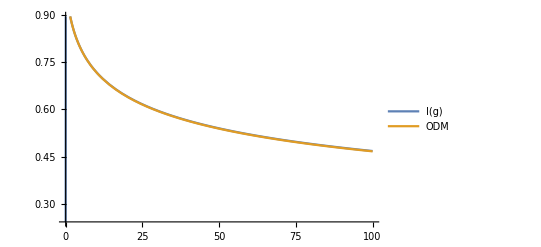

0.00575431

```mathematica
kval = 5;
symbolicQ=False;
odmcoef[kval,ρ];
Flatten[If[symbolicQ, FullSimplify[Solve[%==0, ρ, Reals]], NSolve[%==0, ρ, Reals]]]
ρsol=ρ/.%;
N[ρsol kval]
N[1/ρsol]
odm=Sum[odmcoef[k, ρsol]λ^k, {k,0,kval}];
N[{odmcoef[kval, ρsol],odmcoef[kval+1, ρsol]}]

Simplify[(1-λ)^(1/2)odm /. {λ->(1+2 g/ρsol-√(1+4 g/ρsol))/(2 g/ρsol)}]
Plot[{(ⅇ^(3/4/g) √(3/(2 π)) BesselK[1/4,3/(4 g)])/(√g),%}, {g,0,100}, PlotLegends->{"I(g)", "ODM"}]

(* g->∞ *)
1.6007147824526118 - (ρsol λ)^(1/4) odm /. λ->1
```

### Marino notation

We now consider the order dependent mapping:

g = ρ λ/(1-λ)^2,

where ρ is an adjustable parameter.
Then, from the original integral I(g), we have

```mathematica
(1/Sqrt[2π]) (1-λ)^(1/2) Integrate[Exp[-z^2/2 + λ(z^2/2 - ρ z^4/4)], {z,-∞,∞}]
```

ConditionalExpression[-(ⅇ^((-1+λ)^2/(8 λ ρ)) √(1-λ) (-1+λ) BesselK[1/4,(-1+λ)^2/(8 λ ρ)])/(√(2 π) √(2-2 λ) √(λ ρ)), Re[λ]<1&&Re[λ ρ]>0]

The n-th approximant with ρ=ρ_n is given by

∑_(k=0)^n a_k(ρ_n)λ^k, a_n(ρ_n)=0.

```mathematica
N[Limit[g^(1/4)quarticI[g], g->∞]]
```

1.02277

```mathematica
odmcoef[k_,ρ_]:=If[k==0,1,1/(√(2π)Factorial[k]) Integrate[Exp[-s^2/2](s^2/2-ρ s^4/4)^k, {s,-∞,∞}]]
```

For odd nmax only, we may use
  (N)Solve[%==0, ρ, Reals].
For large nmax, (N)Solve for ρ ∈ Complexes cannot find a “good” solution.
Then, the above assumption, ρ ∈ Reals, is better.

```mathematica
(* For even nmax, ρ ∈ Complexes; Find a maximum value of Abs[ρ] *)
findmaxρ[ρlist_]:= Module[{ρabs},ρabs=Table[Abs[ρ/.%[[i]]], {i,Length[ρlist]}];ρlist[[Position[ρabs, Max[ρabs]][[1,1]]]]]
(* Solver *)
solveρ[coef_,symbolicQ_,complexQ_]:=Module[{solve}, If[symbolicQ, solve=Composition[FullSimplify,Solve], solve=NSolve];Flatten[If[complexQ,
solve[%==0&&Re[ρ]>0&&Im[ρ]≥0, ρ],solve[%==0, ρ,Reals]]]]
```

{ρ→0.00294738+0.0178833 ⅈ,ρ→0.0057082+0.0184488 ⅈ,ρ→0.00821163+0.0185224 ⅈ,ρ→0.0105591+0.0182339 ⅈ,ρ→0.0127693+0.0176401 ⅈ,ρ→0.0148365+0.0167784 ⅈ,ρ→0.016803+0.0156152 ⅈ,ρ→0.0182587,ρ→0.0185227,ρ→0.0197114,ρ→0.019993,ρ→0.0207318,ρ→0.0213616,ρ→0.0213876,ρ→0.0214366,ρ→0.0219547,ρ→0.0221063,ρ→0.0229244,ρ→0.0253938,ρ→0.0254101,ρ→0.0268104,ρ→0.0269537,ρ→0.027235}

ρ→0.027235

0.817049

36.7175

{1.81197×10^-8,-2.5253×10^-8}

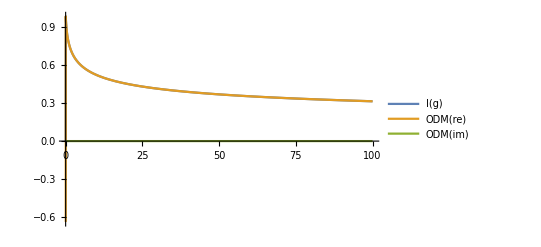

-6.52711×10^-9

```mathematica
kval = 30;
symbolicQ=False; complexQ=True;
odmcoef[kval,ρ];
solveρ[%, symbolicQ,complexQ]
findmaxρ[%]
ρsol=ρ/.%;
N[ρsol kval]
N[1/ρsol]
odm=Sum[odmcoef[k, ρsol]λ^k, {k,0,kval}];
N[{odmcoef[kval, ρsol],odmcoef[kval+1, ρsol]}]

odmg=Simplify[(1-λ)^(1/2)odm /. {λ->(1+2 g/ρsol-√(1+4 g/ρsol))/(2 g/ρsol)}];
Plot[{quarticI[g],Re[odmg], Im[odmg]}, {g,0,100}, PlotLegends->{"I(g)", "ODM(re)", "ODM(im)"}]

(* g->∞ *)
1.0227656721131686 - (ρsol λ)^(1/4) odm /. λ->1
```